```mathematica
FirstValues[tuple_,limit_]:=
Module[
{good, result={},fileName= FileNameForTuple[tuple]},
If[FileExistsQ[fileName],
good= ReadList[fileName,Expression, limit];
If[Length[good] == limit,
result=good
]
];
result
]
```

```mathematica
ListLinePlot[
Sort[
Table[
{N[magicGraham[tuple]],Kurtosis[Map[ DigitRatio[IntegerDigits[#,tuple[[1]]],1]&, FirstValues[tuple,10000]]]},
{tuple,Select[Subsets[Prime[Range[2,25]],{4}],N[magicGraham[#]]>0&]}
]
],
GridLines->Automatic,PlotRange->All
]
```

Kurtosis::vecmat1: Argument {} is neither a non-empty vector nor a non-empty matrix.

General::stop: Further output of Kurtosis will be suppressed during this calculation.

$Aborted

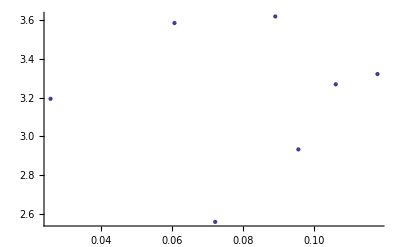

```mathematica
ListPlot[%]
```

```mathematica
Module[
{all =Select[Subsets[Prime[Range[2,11]],{2,4}],N[magicGraham[#]]>0&],result={}, good},
Monitor[
result=Table[
good=FirstValues[tuple,10000];
If[good=={},{},{N[magicGraham[tuple]],N[Kurtosis[Map[ DigitRatio[IntegerDigits[#,tuple[[1]]],1]&, good]]]}]
,{tuple,all}
],
tuple
];
Select[result,#≠{}&]
]
```

{{0.0996804,4.56564},{0.0994625,3.97288},{0.0996002,5.00671},{0.0994116,4.51251},{0.0991845,4.00326},{0.0994537,3.79971},{0.0992313,3.62698},{0.0992603,4.73146},{0.0994056,5.03654},{0.105948,4.16401},{0.107954,4.39836},«7828»,{0.378862,19.1662},{0.38108,4.52778},{0.378832,14.813},{0.38149,7.63265},{0.383708,10.1667},{0.385313,6.19686},{0.379775,21.0744},{0.382433,15.3994},{0.384651,19.3702},{0.386256,24.3956},{0.388884,23.6474}}

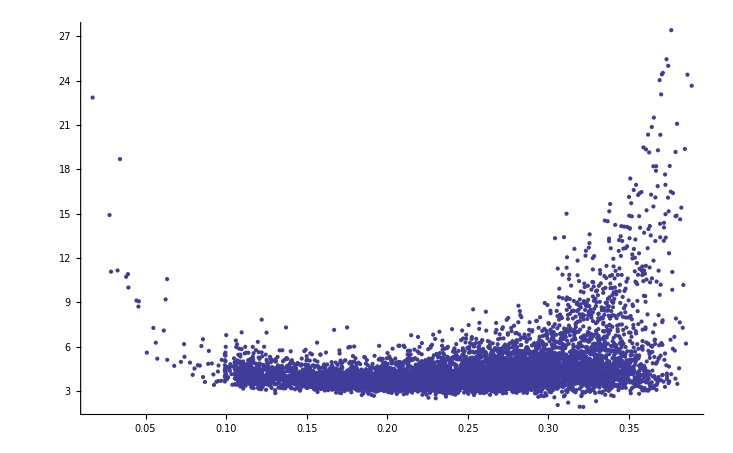

```mathematica
ListPlot[Sort[%]]
```

```mathematica
ccc=Module[
{all =Select[Subsets[Prime[Range[2,25]],{2,5}],N[magicGraham[#]]>0&],result={}, good},
Monitor[
result=Table[
good=FirstValues[tuple,100000];
If[good=={},{},{N[magicGraham[tuple]],N[Kurtosis[Map[ DigitRatio[IntegerDigits[#,tuple[[1]]],1]&, good]]]}]
,{tuple,all}
],
tuple
];
Select[result,#≠{}&]
]
```

$Aborted

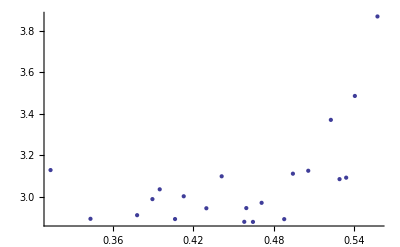

```mathematica
ListPlot[Sort[ccc]]
```